# Ray file import

by Juergen Kanz, November 2021

```mathematica
Clear["Global`*"]
```

## Introduction

Ray files are a typical mean to describe the spatial near-field light distribution of LED and other kinds of light sources for optical design purposes. Non-imaging optics for lighting, automotive, medical devices, and other application areas are more or less the standard now for engineering tasks regarding design.
Near-field photometric and or radiometric measurements are done with special equipment from Radiant Vision Systems or TechnoTeam. Both companies have their software products to transform the measured data into application formats for optical design software.

The intention for this notebook is to show a way to import ASCII ray files as distributed by LED manufacturers for their products. The files for specific optic design software are typically stored as binary files without public available format descriptions.

Due to the high documentation level of OSRAM semiconductors, I decided to take a ray file package from this company.

## Download OSRAM files for optical simulation

Download of the chosen LED OSRAM ray File package via https://www.osram.com/apps/downloadcenter/?path=%2Fos-files%2FOptical+Simulation%2FLED/OSCONIQ/OSCONIQ%20E/OSCONIQ%20E2835/GW%20QTLQS1.LM. Select an ASCII file (either _ASCII.zip or _TraceProText.zip).

-Graphics-

In case the user takes the _TraceProText file, the general process as described below remains the same. The difference is to skip some header lines before the pure data as discussed below can be processed.

The downloaded ASCII Zip-file contains the following datasets:

-Graphics-

```mathematica
TextGrid[{{" ", " "},
{"rayfile_GW_QTLQS1...yellow...500k...ASCII","a ray dataset with 500 000 yellow rays in ASCII"},{"rayfile_GW_QTLQS1...blue...100k...ASCII","a ray dataset with 100 000 blue rays in ASCII"},{"rayfile_GW_QTLQS1...blue...5M...ASCII","a ray dataset with 5 000 000 blue rays in ASCII"},
{" ", " "},
{"GW_QTLQS1..._info.pdf","a Pdf file with important technical information about the LED"},
{"GW_QTLQS1..._geometry","CAD files with LED geometry in different formats"},
{" ", " "},
{"W_QTLQS1..._yellow..._spectrum","a spectrum data file of the yellow rays"},
{" ", " "}}]
```

|  
rayfile_GW_QTLQS1...yellow...500k...ASCII | a ray dataset with 500 000 yellow rays in ASCII
rayfile_GW_QTLQS1...blue...100k...ASCII | a ray dataset with 100 000 blue rays in ASCII
rayfile_GW_QTLQS1...blue...5M...ASCII | a ray dataset with 5 000 000 blue rays in ASCII
  |  
GW_QTLQS1..._info.pdf | a Pdf file with important technical information about the LED
GW_QTLQS1..._geometry | CAD files with LED geometry in different formats
  |  
W_QTLQS1..._yellow..._spectrum | a spectrum data file of the yellow rays
  |

## Import Spectral Intensity Distributions

The spectra of OSRAM Opto Semiconductors white LEDs have at least two local maxima due to the specific generation of white light. The peak in the blue wavelength range has a narrow width and a peak wavelength around 450 nm. The peak in the yellow wavelength range has a wider distribution with a peak wavelength around 540 – 600 nm, depending on the LED type.
Due to the different angular characteristics of rays in the “blue” and “yellow” parts of the spectrum, a separation of the ray model into two parts is necessary.
Therefore, two ray files are delivered with each white LED, one ray file for the blue and one ray file for the yellow part of the spectrum. Both ray files have the same global coordinate origin and must be placed in the simulation software at exactly the same (x,y,z) coordinates. To use the ray files in a simulation, the user has to consider the following points:

“Blue” and “yellow” ray files must be placed at the same (x,y,z) coordinates.

Simulation should run simultaneously for the two ray files, as for two overlapping sources.

The luminous flux contributions of both ray files must be set appropriately.

The peak wavelength is defined as the single wavelength where the radiometric emission spectrum of the light source reaches its maximum. More simply, it does not represent any perceived emission of the light source by the human eye, but rather by photo-detectors.

The dominant wavelength is defined as the single wavelength that is perceived by the human eye. Generally one light source consists of multiple wavelength spectra from the light source rather than one single wavelength. Our brains turn those multiple spectra into a single color of light consistent with a single specific wavelength which is what we see when we look at the light. That’s the light source’s Dominant wavelength.

### Import of the “Blue” spectra

```mathematica
(* Path to be modified *)
spectrumBlue=Import["e:\\Users\\juerg\\Documents\\Mathematica\\Light&Optics\\RayfileImport\\GW_QTLQS1_LM_4000K_blue_20210611_spectrum.txt","Data"];
```

Find the peak in the “Blue” spectrum. Results are in “Nanometers”

```mathematica
pos=First@Flatten[Position[spectrumBlue,Max[spectrumBlue[[All,2]]]]];
```

```mathematica
lambdaMaxBlue=spectrumBlue[[pos,1]]
```

470.

### Import of the “Yellow” spectra

```mathematica
(* Path to be modified *)
spectrumYellow=Import["e:\\Users\\juerg\\Documents\\Mathematica\\Light&Optics\\RayfileImport\\GW_QTLQS1_LM_4000K_yellow_20210611_spectrum.txt","Data"];
```

Find the peak in the “Yellow” spectrum. Results are in “Nanometers”

```mathematica
pos=First@Flatten[Position[spectrumYellow,Max[spectrumYellow[[All,2]]]]];
```

```mathematica
lambdaMaxYellow =spectrumYellow[[pos,1]]
```

594.

### Spectrum Plot

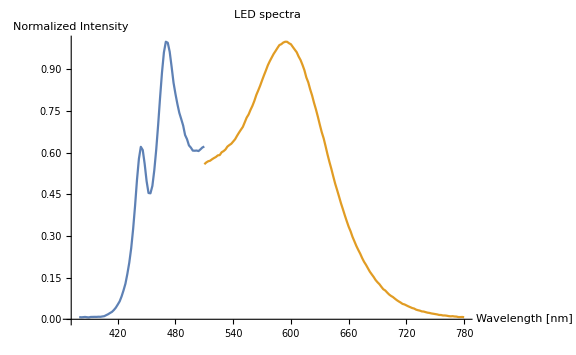

```mathematica
ListLinePlot[{spectrumBlue,spectrumYellow},PlotLabel->"LED spectra",AxesLabel->{"Wavelength [nm]","Normalized Intensity"},ImageSize->Large]
```

Due to the separate handling of the “Blue” and “Yellow” spectra, in line with a normalization, the result is not acceptable for a full spectrum.

The following image is taken from “GW_QTLQS1_LM_20210611_info.pdf” which is part of the zip-file and shows the full spectrum.
-Graphics-

The two spectra have to be aligned with OSRAM picture for a full spectrum, which can be used for further processing.

```mathematica
lastBlue=Last@spectrumBlue
```

{510.,0.6224}

```mathematica
firstYellow=First@spectrumYellow
```

{510.,0.5587}

```mathematica
factor=firstYellow[[2]]/lastBlue[[2]]
```

0.897654

The factor here is finally a correction factor for the spectra alignment.

```mathematica
adjustedBlueSpectrum=spectrumBlue;
```

We multiply the intensities of the blue rays with the factor for alignment.

```mathematica
adjustedBlueSpectrum[[All,2]]=spectrumBlue[[All,2]]*factor;
```

```mathematica
spectrumYellow=Rest[spectrumYellow];
```

```mathematica
ledFullSpectrum=Union[adjustedBlueSpectrum,spectrumYellow];
```

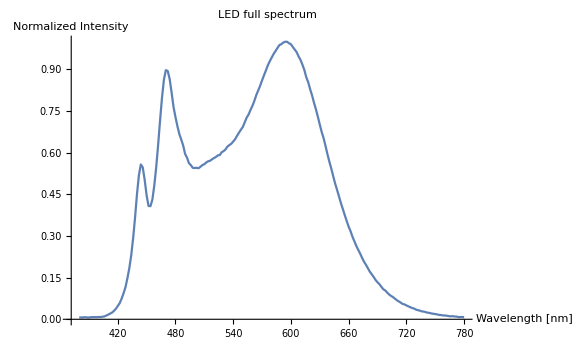

```mathematica
ListLinePlot[{ledFullSpectrum},PlotLabel->"LED full spectrum",AxesLabel->{"Wavelength [nm]","Normalized Intensity"},ImageSize->Large]
```

Now we have a full spectrum of the LED.

Save the ledFullSpectrum as a CSV file and make use of it in a spectrum analysis software/notebook.

```mathematica
Export["ledFullSpectrum.csv",ledFullSpectrum]
```

ledFullSpectrum.csv

## Load photometric rays

### Import Blue-Rays

The following line of code shows how to import a blue ray dataset with 100k rays. It is not a problem to read the 5M (5 million) ray files as well with Mathematica.

```mathematica
(* Path has to be modified *)
rawdata=Import["e:\\Users\\juerg\\Documents\\Mathematica\\Light&Optics\\RayfileImport\\rayfile_GW_QTLQS1_LM_blue_100k_20210611_ASCII.TXT","Table"];
```

```mathematica
rawdata[[1]]
```

{X_Pos,Y_Pos,Z_Pos,X_Vec,Y_Vec,Z_Vec,Flux}

```mathematica
TextGrid[{{"Explanation:", " "},
{"X_Pos","The origin x coordinate of a ray"},
{"Y_Pos","The origin y coordinate of a ray"},
{"Z_Pos","The origin z coordinate of a ray"},
{" ", " "},
{"X_Vec","The x coordinate of the direction vector"},
{"Y_Vec","The y coordinate of the direction vector"},
{"Z_Vec","The z coordinate of the direction vector"},
{" ", " "},
{"Flux","The energy of the ray"},
{" ", " "}}]
```

Explanation: |  
X_Pos | The origin x coordinate of a ray
Y_Pos | The origin y coordinate of a ray
Z_Pos | The origin z coordinate of a ray
  |  
X_Vec | The x coordinate of the direction vector
Y_Vec | The y coordinate of the direction vector
Z_Vec | The z coordinate of the direction vector
  |  
Flux | The energy of the ray
  |

It is not possible to work with underline characters in column names, hence we take them out.

```mathematica
header={"Xpos","Ypos","Zpos","Xvec","Yvec","Zvec","Flux"}
```

{Xpos,Ypos,Zpos,Xvec,Yvec,Zvec,Flux}

#### Simplified drawing of a vector from {Xpos,Ypos,Zpos} to {Xvec,Yvec,Zvec}

```mathematica
orig={0,0,0};              (* Xpos, Ypos, Zpos *)
axes={{1,0,0},{0,1,0},{0,0,1}};      (* Coordinate system *)
pt={0.5,0.5,0.5};    (* Xvec, Yvec, Zvec *)
Graphics3D[{Arrow[{orig,#}]&/@axes,{Red,Arrow[{orig,pt}]}},Boxed->False]
```

-Graphics3D-

#### Import Blue-Rays Part 2

```mathematica
rawdata2=Rest[rawdata];
```

All vector data are scaled, just to make them visible in the 3D graphic below.

```mathematica
scaler=3;
rawdata2[[All,4]]=rawdata2[[All,4]]*scaler;
rawdata2[[All,5]]=rawdata2[[All,5]]*scaler;
rawdata2[[All,6]]=rawdata2[[All,6]]*scaler;
```

Get a blue ray dataset

```mathematica
blueRays=AssociationThread[header->#]&/@Rest[rawdata2]//Dataset;
```

### Import Yellow-Rays

```mathematica
(* Path has to be modified *)
rawdata=Import["e:\\Users\\juerg\\Documents\\Mathematica\\Light&Optics\\RayfileImport\\rayfile_GW_QTLQS1_LM_yellow_100k_20210611_ASCII.TXT","Table"];
```

```mathematica
rawdata2=Rest[rawdata];
```

All vector data are scaled, just to make them visible in the 3D graphic below.

```mathematica
scaler=3;
rawdata2[[All,4]]=rawdata2[[All,4]]*scaler;
rawdata2[[All,5]]=rawdata2[[All,5]]*scaler;
rawdata2[[All,6]]=rawdata2[[All,6]]*scaler;
```

Get a yellow ray dataset

```mathematica
yellowRays=AssociationThread[header->#]&/@Rest[rawdata2]//Dataset;
```

Household-keeping

```mathematica
Clear[rawdata,rawdata2];
```

### Few data from the ray data

The total number of rays loaded:

```mathematica
numRays=Length[blueRays]+Length[yellowRays]
```

199998

Energy sum of all yellow rays:

```mathematica
yellowFlux=Query[Total,"Flux"]@yellowRays
```

0.272937

Energy sum of all blue rays:

```mathematica
blueFlux=Query[Total,"Flux"]@blueRays
```

0.194883

```mathematica
energyOfRays=yellowFlux+blueFlux
```

0.46782

According to the info.pdf  the LED has a total LED Luminous flux of  ϕ_v= 144 Lumen. Flux is set to a default of 131.39/12.11 the user has to adapt the flux setting with new factors.

## Import CAD File of the LED Housing

Many LED suppliers provide CAD-Files with the geometry of their products. The files are typically available in the following formats:

.SLDPRT - SolidWorks Part file

.IGS - Initial Graphics Exchange Specification

.STEP - Standard for the exchange of product model data

I tried to import the STEP file into Mathematica with the OpenCascadeLink, but unfortunately, I failed. Hence, I imported the CAD-file in Rhino 3D and converted it into the common STL format for import.

```mathematica
(* Path has to be modified *)
ledhousing=Import["e:\\Users\\juerg\\Documents\\Mathematica\\Light&Optics\\RayfileImport\\led.stl","STL"]
```

-Graphics3D-

## 3D Graphics

The rays are already randomly stored in the ray files. Hence, no additional shuffling is needed. For the graphical presentation, only fifty blue and yellow rays are randomly taken.

```mathematica
blueRandomRays=RandomChoice[blueRays,50];
```

```mathematica
yellowRandomRays=RandomChoice[yellowRays,50];
```

```mathematica
yellowLines=Table[Line[{{yellowRandomRays[[i,1]],yellowRandomRays[[i,2]],yellowRandomRays[[i,3]]},{yellowRandomRays[[i,4]],yellowRandomRays[[i,5]],yellowRandomRays[[i,6]]}}],{i,1,Length[yellowRandomRays]}];
```

```mathematica
blueLines=Table[Line[{{blueRandomRays[[i,1]],blueRandomRays[[i,2]],blueRandomRays[[i,3]]},{blueRandomRays[[i,4]],blueRandomRays[[i,5]],blueRandomRays[[i,6]]}}],{i,1,Length[blueRandomRays]}];
```

```mathematica
Graphics3D[{ledhousing,Blue,Thick,blueLines,Yellow,Thick,yellowLines},Boxed->False,PlotLabel->"Forward Ray Tracing"]
```

-Graphics3D-

## Summary

The author shows ways to import rays from ASCII files. Even the import of two times 5M rays was not a constraint to process the data. The next step could be the development of an environment for (forward) ray tracing to use Mathematica in the field of non-imaging optics with non-sequential ray tracing as well.

## Resources

OSRAM Product Page, https://www.osram.com/ecat/OSCONIQ%C2%AE%20E%202835%20GW%20QTLQS1.LM/com/en/class_pim_web_catalog_103489/prd_pim_device_18726922/, Last accessed 11/24/2021

OSRAM RayFile Package for chosen LED, https://www.osram.com/apps/downloadcenter/?path=%2Fos-files%2FOptical+Simulation%2FLED/OSCONIQ/OSCONIQ%20E/OSCONIQ%20E2835/GW%20QTLQS1.LM, select: “rayfile_GW_QTLQS1_LM_20210611_ASCII.zip”, Last accessed 11/24/2021

Wolfram Mathworld, “Direction cosine”, https://mathworld.wolfram.com/DirectionCosine.html, Last accessed 11/24/2021

TechnoTeam Homepage, https://www.technoteam.de/, Last accessed 11/24/2021

Radiant Vision Systems, https://www.radiantvisionsystems.com/, Last accessed 11/24/2021